```mathematica
FinancialData["^SPX","Close",{{2019},{2020}}]
```

TimeSeries[…]

```mathematica
rats=Ratios[Out[1]["Values"]]
```

{0.975243,1.03434,1.00701,1.0097,1.0041,1.00452,0.999854,0.994742,1.01072,1.00222,1.00759,1.01318,0.985843,1.0022,1.00138,1.00849,0.992153,0.998544,1.01555,1.0086,1.0009,1.00678,1.00471,0.997776,0.990643,1.00068,1.00071,1.01289,1.00302,0.997348,1.01088,1.0015,1.00178,0.996474,1.00641,1.00123,0.99921,0.999456,0.997174,1.0069,0.996119,0.998868,0.993476,0.991874,0.997868,1.01467,1.00295,1.00695,0.999132,1.00498,1.00371,0.999869,0.997056,1.01085,0.981025,0.999161,1.00718,0.995356,1.00359,1.00673,1.01157,1.00002,1.00215,1.00208,1.00464,1.00105,0.993933,1.00348,1.00004,1.00661,0.999371,1.00051,0.997726,1.00158,1.00101,1.00884,0.997808,0.999631,1.00469,1.00107,1.00095,0.992498,0.997876,1.00964,0.995529,0.983488,0.998395,0.996979,1.00372,0.975869,1.00802,1.00584,1.0089,0.994163,0.993251,1.0085,0.997176,0.988086,1.00135,0.991624,0.993088,1.0021,0.986805,0.997235,1.02143,1.00816,1.00614,1.0105,1.00466,0.99965,0.997962,1.0041,0.998388,1.00093,1.00972,1.00299,1.00947,0.998741,0.998268,0.990504,0.998766,1.00382,1.00576,1.00767,1.00293,1.00171,1.00596,0.998194,0.995165,1.00124,1.00451,1.00229,1.00462,1.00018,0.996596,0.993469,1.00358,0.993823,1.00283,1.00685,1.00469,0.994738,1.00739,0.998384,0.997421,0.989114,0.991001,0.992717,0.970222,1.01302,1.00077,1.01876,0.993383,0.987683,1.01513,0.970707,1.00246,1.01443,1.01211,0.992085,1.00825,0.999494,0.974054,1.01098}

```mathematica
Min@rats
```

0.970222

```mathematica
Max@rats
```

1.03434

```mathematica
{Min@Out[1]["Values"],Max@Out[1]["Values"]}
```

{2447.89,3025.86}

```mathematica
diff=Differences[Out[1]["Values"]]
```

{-62.1401,84.05,17.75,24.72,10.55,11.6799,-0.379883,-13.6499,27.6899,5.80005,19.8599,34.75,-37.8101,5.80005,3.63013,22.4299,-20.9099,-3.8501,41.05,23.05,2.42993,18.3401,12.8298,-6.08984,-25.5601,1.82983,1.92017,34.9299,8.30005,-7.30005,29.8701,4.15991,4.93994,-9.82007,17.79,3.44019,-2.21021,-1.52002,-7.88989,19.2,-10.8799,-3.16016,-18.2,-22.52,-5.85986,40.23,8.21997,19.3999,-2.43994,14.,10.46,-0.369873,-8.34009,30.6499,-54.1699,-2.34985,20.0999,-13.0898,10.0698,18.96,32.79,0.0500488,6.15991,5.98999,13.3501,3.03003,-17.5701,10.01,0.110107,19.0898,-1.82983,1.47998,-6.61011,4.58008,2.93994,25.71,-6.42993,-1.08008,13.71,3.15015,2.80005,-22.1001,-6.20996,28.1199,-13.1699,-48.4199,-4.63013,-8.69995,10.6799,-69.5298,22.5398,16.55,25.3601,-16.79,-19.3,24.1301,-8.09009,-34.03,3.82007,-23.6702,-19.3699,5.84009,-36.8,-7.61011,58.8201,22.8799,17.3401,29.8501,13.3899,-1.01001,-5.87988,11.7998,-4.65991,2.68994,28.0801,8.70996,27.72,-3.71997,-5.10986,-27.9702,-3.59985,11.1399,16.8401,22.5701,8.67993,5.07007,17.74,-5.41016,-14.46,3.67993,13.4402,6.83984,13.8601,0.530029,-10.26,-19.6201,10.6902,-18.5,8.41992,20.4399,14.0901,-15.8901,22.1902,-4.89014,-7.79004,-32.8,-26.8198,-21.51,-87.3101,37.03,2.20996,54.1101,-19.4402,-35.95,43.6201,-85.72,7.,41.0798,34.97,-23.1399,23.9199,-1.47998,-75.8398,31.2698}

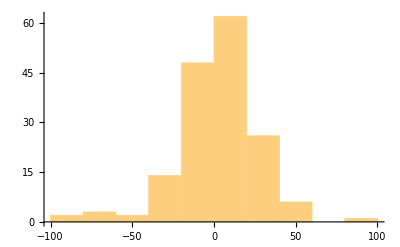

```mathematica
Histogram[diff]
```

```mathematica
Abs[diff]
```

{62.1401,84.05,17.75,24.72,10.55,11.6799,0.379883,13.6499,27.6899,5.80005,19.8599,34.75,37.8101,5.80005,3.63013,22.4299,20.9099,3.8501,41.05,23.05,2.42993,18.3401,12.8298,6.08984,25.5601,1.82983,1.92017,34.9299,8.30005,7.30005,29.8701,4.15991,4.93994,9.82007,17.79,3.44019,2.21021,1.52002,7.88989,19.2,10.8799,3.16016,18.2,22.52,5.85986,40.23,8.21997,19.3999,2.43994,14.,10.46,0.369873,8.34009,30.6499,54.1699,2.34985,20.0999,13.0898,10.0698,18.96,32.79,0.0500488,6.15991,5.98999,13.3501,3.03003,17.5701,10.01,0.110107,19.0898,1.82983,1.47998,6.61011,4.58008,2.93994,25.71,6.42993,1.08008,13.71,3.15015,2.80005,22.1001,6.20996,28.1199,13.1699,48.4199,4.63013,8.69995,10.6799,69.5298,22.5398,16.55,25.3601,16.79,19.3,24.1301,8.09009,34.03,3.82007,23.6702,19.3699,5.84009,36.8,7.61011,58.8201,22.8799,17.3401,29.8501,13.3899,1.01001,5.87988,11.7998,4.65991,2.68994,28.0801,8.70996,27.72,3.71997,5.10986,27.9702,3.59985,11.1399,16.8401,22.5701,8.67993,5.07007,17.74,5.41016,14.46,3.67993,13.4402,6.83984,13.8601,0.530029,10.26,19.6201,10.6902,18.5,8.41992,20.4399,14.0901,15.8901,22.1902,4.89014,7.79004,32.8,26.8198,21.51,87.3101,37.03,2.20996,54.1101,19.4402,35.95,43.6201,85.72,7.,41.0798,34.97,23.1399,23.9199,1.47998,75.8398,31.2698}

```mathematica
Total[%8]
```

2910.81

```mathematica
Accumulate[%8]
```

{62.1401,146.19,163.94,188.66,199.21,210.89,211.27,224.92,252.61,258.41,278.27,313.02,350.83,356.63,360.26,382.69,403.6,407.45,448.5,471.55,473.98,492.32,505.15,511.24,536.8,538.63,540.55,575.48,583.78,591.08,620.95,625.11,630.05,639.87,657.66,661.1,663.31,664.83,672.72,691.92,702.8,705.96,724.16,746.68,752.54,792.77,800.99,820.39,822.83,836.83,847.29,847.66,856.,886.65,940.82,943.169,963.269,976.359,986.429,1005.39,1038.18,1038.23,1044.39,1050.38,1063.73,1066.76,1084.33,1094.34,1094.45,1113.54,1115.37,1116.85,1123.46,1128.04,1130.98,1156.69,1163.12,1164.2,1177.91,1181.06,1183.86,1205.96,1212.17,1240.29,1253.46,1301.88,1306.51,1315.21,1325.89,1395.42,1417.96,1434.51,1459.87,1476.66,1495.96,1520.09,1528.18,1562.21,1566.03,1589.7,1609.07,1614.91,1651.71,1659.32,1718.14,1741.02,1758.36,1788.21,1801.6,1802.61,1808.49,1820.29,1824.95,1827.64,1855.72,1864.43,1892.15,1895.87,1900.98,1928.95,1932.55,1943.69,1960.53,1983.1,1991.78,1996.85,2014.59,2020.,2034.46,2038.14,2051.58,2058.42,2072.28,2072.81,2083.07,2102.69,2113.38,2131.88,2140.3,2160.74,2174.83,2190.72,2212.91,2217.8,2225.59,2258.39,2285.21,2306.72,2394.03,2431.06,2433.27,2487.38,2506.82,2542.77,2586.39,2672.11,2679.11,2720.19,2755.16,2778.3,2802.22,2803.7,2879.54,2910.81}

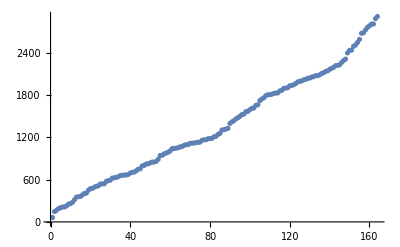

```mathematica
ListPlot[%10]
```

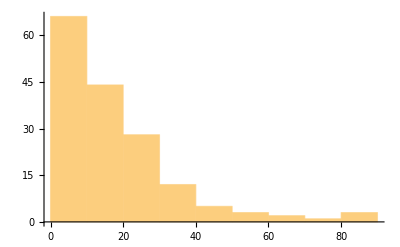

```mathematica
Histogram[%8]
```

```mathematica
Max[Out[10]]
```

2910.81

```mathematica
Min[Out[10]]
```

62.1401

```mathematica
PercentForm@(Max[Out[10]]/Min[Out[10]])
```

4684%

```mathematica
100(Max[Out[10]]-Min[Out[10]])
```

284867.

```mathematica
CountryData["UnitedStates",{"InflationRate",All}]
```

TimeSeries[…]

```mathematica
Histogram3D@
Out[17]["Values"]
```

Histogram3D::ldata: StructuredArray[QuantityArray,{38},StructuredArray`StructuredData[QuantityArray,{0.0499088,0.0423121,0.0557773,0.0902887,0.0944886,0.0575139,0.0634455,0.0702634,0.0830702,«21»,0.0240881,0.0175005,0.0213105,0.0287257,0.0326351,0.0321724,0.0268834,0.0145036},1/(…s),{{1}}]] is not a valid dataset or list of datasets.

Histogram3D[QuantityArray[…]]

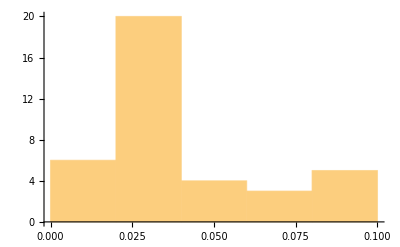

```mathematica
Histogram@
Out[17]["Values"]
```

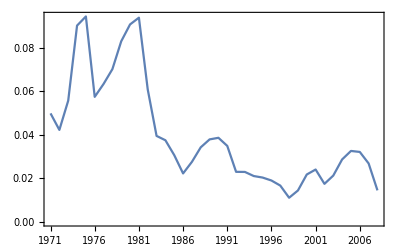

```mathematica
DateListPlot@Out[17]
```

```mathematica
GeometricMean@Out[17]["Values"]
```

0.0339398 per year

```mathematica
Fold[Times,Out[17]["Values"]]
```

Fold::normal: Nonatomic expression expected at position 2 in Fold[Times,StructuredArray[QuantityArray,{38},StructuredArray`StructuredData[QuantityArray,{0.0499088,0.0423121,0.0557773,0.0902887,0.0944886,0.0575139,0.0634455,0.0702634,«22»,0.0240881,0.0175005,0.0213105,0.0287257,0.0326351,0.0321724,0.0268834,0.0145036},1/Years,{{1}}]]].

Fold[Times,QuantityArray[…]]

```mathematica
Fold[Times,100,Out[17]["Values"]]
```

Fold::normal: Nonatomic expression expected at position 3 in Fold[Times,100,StructuredArray[QuantityArray,{38},StructuredArray`StructuredData[QuantityArray,{0.0499088,0.0423121,0.0557773,0.0902887,0.0944886,0.0575139,0.0634455,0.0702634,«22»,0.0240881,0.0175005,0.0213105,0.0287257,0.0326351,0.0321724,0.0268834,0.0145036},1/Years,{{1}}]]].

Fold[Times,100,QuantityArray[…]]

```mathematica
Out[17]["Values"]
```

QuantityArray[…]

```mathematica
Map[QuantityMagnitude,Out[17]["Values"]]
```

{0.0499088,0.0423121,0.0557773,0.0902887,0.0944886,0.0575139,0.0634455,0.0702634,0.0830702,0.0908216,0.0939243,0.0609088,0.0395455,0.0375504,0.0306966,0.0222927,0.0276107,0.0343012,0.0379449,0.0386782,0.0349598,0.0230273,0.0229747,0.0210903,0.0203923,0.0190374,0.0167035,0.0111104,0.0144494,0.0217986,0.0240881,0.0175005,0.0213105,0.0287257,0.0326351,0.0321724,0.0268834,0.0145036}

```mathematica
Fold[Times,100,Out[25]]
```

1.46879×10^-54

```mathematica
Fold[Times,{100},Out[25]]
```

{1.46879×10^-54}

```mathematica
GeometricMean@Out[25]
```

0.0339398

```mathematica
PercentForm@
GeometricMean@
Out[25]
```

3.394%

```mathematica
2
```

2

```mathematica
4
```

4

```mathematica
With[{
spx=FinancialData["^SPX","Close",{{2019},{2020}}],
vix=FinancialData["VIX","Close",{{2019},{2020}}]
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
{First@First@f,Correlation[First/@Last/@f,Last/@Last/@f]}
,{f,secondtable}]
},
corr
]
]
]
]
]
]
]
]
```

First::normal: Nonatomic expression expected at position 1 in First[-8.].

Last::normal: Nonatomic expression expected at position 1 in Last[-8.].

First::normal: Nonatomic expression expected at position 1 in First[-8.].

Last::normal: Nonatomic expression expected at position 1 in Last[-8.].

First::normal: Nonatomic expression expected at position 1 in First[-8.].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[-8.].

General::stop: Further output of Last::normal will be suppressed during this calculation.

{{{2019,1,2,0,0,0.},((-0.00222199+Conjugate[Last[-8.]]) (0.0247567+First[-8.]))/(√((0.0247567+Conjugate[First[-8.]]) (0.0247567+First[-8.])) √((-0.00222199+1) 1))},150,{{2019,8,12,0,0,0.},((1) 1)/(√1 1)}}
 |  |  |  |

```mathematica
With[{
spx=FinancialData["^SPX","Close",{{2019},{2020}}],
vix=FinancialData["VIX","Close",{{2019},{2020}}]
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
secondtable
]
]
]
]
]
]
]
```

{{Wed 2 Jan 2019 00:00:00GMT-8.,{{0.096038,-0.159921,0.000935475,-0.043458,-0.0239375,-0.024024,-0.0671795,0.0483782,-0.024646,0.0236559},{-0.0247567,0.0343357,0.00701043,0.00969529,0.00409805,0.00451842,-0.000146298,-0.00525753,0.0107217,0.00222199}}},{Thu 3 Jan 2019 00:00:00GMT-8.,{{-0.159921,0.000935475,-0.043458,-0.0239375,-0.024024,-0.0671795,0.0483782,-0.024646,0.0236559,-0.0514707},{0.0343357,0.00701043,0.00969529,0.00409805,0.00451842,-0.000146298,-0.00525753,0.0107217,0.00222199,0.0075914}}},{Fri 4 Jan 2019 00:00:00GMT-8.,{{0.000935475,-0.043458,-0.0239375,-0.024024,-0.0671795,0.0483782,-0.024646,0.0236559,-0.0514707,-0.0143965},{0.00701043,0.00969529,0.00409805,0.00451842,-0.000146298,-0.00525753,0.0107217,0.00222199,0.0075914,0.0131831}}},{Mon 7 Jan 2019 00:00:00GMT-8.,{{-0.043458,-0.0239375,-0.024024,-0.0671795,0.0483782,-0.024646,0.0236559,-0.0514707,-0.0143965,0.168539},{0.00969529,0.00409805,0.00451842,-0.000146298,-0.00525753,0.0107217,0.00222199,0.0075914,0.0131831,-0.0141573}}},{Tue 8 Jan 2019 00:00:00GMT-8.,{{-0.0239375,-0.024024,-0.0671795,0.0483782,-0.024646,0.0236559,-0.0514707,-0.0143965,0.168539,-0.0615384},{0.00409805,0.00451842,-0.000146298,-0.00525753,0.0107217,0.00222199,0.0075914,0.0131831,-0.0141573,0.00220291}}},{Wed 9 Jan 2019 00:00:00GMT-8.,{{-0.024024,-0.0671795,0.0483782,-0.024646,0.0236559,-0.0514707,-0.0143965,0.168539,-0.0615384,-0.0322746},{0.00451842,-0.000146298,-0.00525753,0.0107217,0.00222199,0.0075914,0.0131831,-0.0141573,0.00220291,0.00137573}}},{Thu 10 Jan 2019 00:00:00GMT-8.,{{-0.0671795,0.0483782,-0.024646,0.0236559,-0.0514707,-0.0143965,0.168539,-0.0615384,-0.0322746,-0.0778189},{-0.000146298,-0.00525753,0.0107217,0.00222199,0.0075914,0.0131831,-0.0141573,0.00220291,0.00137573,0.00848869}}},{Fri 11 Jan 2019 00:00:00GMT-8.,{{0.0483782,-0.024646,0.0236559,-0.0514707,-0.0143965,0.168539,-0.0615384,-0.0322746,-0.0778189,0.0832377},{-0.00525753,0.0107217,0.00222199,0.0075914,0.0131831,-0.0141573,0.00220291,0.00137573,0.00848869,-0.00784683}}},{Mon 14 Jan 2019 00:00:00GMT-8.,{{-0.024646,0.0236559,-0.0514707,-0.0143965,0.168539,-0.0615384,-0.0322746,-0.0778189,0.0832377,0.0137784},{0.0107217,0.00222199,0.0075914,0.0131831,-0.0141573,0.00220291,0.00137573,0.00848869,-0.00784683,-0.00145625}}},{Tue 15 Jan 2019 00:00:00GMT-8.,{{0.0236559,-0.0514707,-0.0143965,0.168539,-0.0615384,-0.0322746,-0.0778189,0.0832377,0.0137784,-0.0768426},{0.00222199,0.0075914,0.0131831,-0.0141573,0.00220291,0.00137573,0.00848869,-0.00784683,-0.00145625,0.0155493}}},{Wed 16 Jan 2019 00:00:00GMT-8.,{{-0.0514707,-0.0143965,0.168539,-0.0615384,-0.0322746,-0.0778189,0.0832377,0.0137784,-0.0768426,-0.0617214},{0.0075914,0.0131831,-0.0141573,0.00220291,0.00137573,0.00848869,-0.00784683,-0.00145625,0.0155493,0.0085974}}},{Thu 17 Jan 2019 00:00:00GMT-8.,{{-0.0143965,0.168539,-0.0615384,-0.0322746,-0.0778189,0.0832377,0.0137784,-0.0768426,-0.0617214,-0.0259505},{0.0131831,-0.0141573,0.00220291,0.00137573,0.00848869,-0.00784683,-0.00145625,0.0155493,0.0085974,0.00089861}}},{Fri 18 Jan 2019 00:00:00GMT-8.,{{0.168539,-0.0615384,-0.0322746,-0.0778189,0.0832377,0.0137784,-0.0768426,-0.0617214,-0.0259505,-0.0254027},{-0.0141573,0.00220291,0.00137573,0.00848869,-0.00784683,-0.00145625,0.0155493,0.0085974,0.00089861,0.00677624}}},{Tue 22 Jan 2019 00:00:00GMT-8.,{{-0.0615384,-0.0322746,-0.0778189,0.0832377,0.0137784,-0.0768426,-0.0617214,-0.0259505,-0.0254027,-0.0101716},{0.00220291,0.00137573,0.00848869,-0.00784683,-0.00145625,0.0155493,0.0085974,0.00089861,0.00677624,0.00470842}}},{Wed 23 Jan 2019 00:00:00GMT-8.,{{-0.0322746,-0.0778189,0.0832377,0.0137784,-0.0768426,-0.0617214,-0.0259505,-0.0254027,-0.0101716,0.100193},{0.00137573,0.00848869,-0.00784683,-0.00145625,0.0155493,0.0085974,0.00089861,0.00677624,0.00470842,-0.00222444}}},{Thu 24 Jan 2019 00:00:00GMT-8.,{{-0.0778189,0.0832377,0.0137784,-0.0768426,-0.0617214,-0.0259505,-0.0254027,-0.0101716,0.100193,-0.0443665},{0.00848869,-0.00784683,-0.00145625,0.0155493,0.0085974,0.00089861,0.00677624,0.00470842,-0.00222444,-0.00935714}}},{Fri 25 Jan 2019 00:00:00GMT-8.,{{0.0832377,0.0137784,-0.0768426,-0.0617214,-0.0259505,-0.0254027,-0.0101716,0.100193,-0.0443665,-0.0397068},{-0.00784683,-0.00145625,0.0155493,0.0085974,0.00089861,0.00677624,0.00470842,-0.00222444,-0.00935714,0.000676201}}},{Mon 28 Jan 2019 00:00:00GMT-8.,{{0.0137784,-0.0768426,-0.0617214,-0.0259505,-0.0254027,-0.0101716,0.100193,-0.0443665,-0.0397068,0.0159033},{-0.00145625,0.0155493,0.0085974,0.00089861,0.00677624,0.00470842,-0.00222444,-0.00935714,0.000676201,0.000709103}}},{Tue 29 Jan 2019 00:00:00GMT-8.,{{-0.0768426,-0.0617214,-0.0259505,-0.0254027,-0.0101716,0.100193,-0.0443665,-0.0397068,0.0159033,-0.0338134},{0.0155493,0.0085974,0.00089861,0.00677624,0.00470842,-0.00222444,-0.00935714,0.000676201,0.000709103,0.0128902}}},{Wed 30 Jan 2019 00:00:00GMT-8.,{{-0.0617214,-0.0259505,-0.0254027,-0.0101716,0.100193,-0.0443665,-0.0397068,0.0159033,-0.0338134,0.0142579},{0.0085974,0.00089861,0.00677624,0.00470842,-0.00222444,-0.00935714,0.000676201,0.000709103,0.0128902,0.00302399}}},{Thu 31 Jan 2019 00:00:00GMT-8.,{{-0.0259505,-0.0254027,-0.0101716,0.100193,-0.0443665,-0.0397068,0.0159033,-0.0338134,0.0142579,0.0364217},{0.00089861,0.00677624,0.00470842,-0.00222444,-0.00935714,0.000676201,0.000709103,0.0128902,0.00302399,-0.00265164}}},{Fri 1 Feb 2019 00:00:00GMT-8.,{{-0.0254027,-0.0101716,0.100193,-0.0443665,-0.0397068,0.0159033,-0.0338134,0.0142579,0.0364217,-0.0807645},{0.00677624,0.00470842,-0.00222444,-0.00935714,0.000676201,0.000709103,0.0128902,0.00302399,-0.00265164,0.0108788}}},{Mon 4 Feb 2019 00:00:00GMT-8.,{{-0.0101716,0.100193,-0.0443665,-0.0397068,0.0159033,-0.0338134,0.0142579,0.0364217,-0.0807645,-0.00201205},{0.00470842,-0.00222444,-0.00935714,0.000676201,0.000709103,0.0128902,0.00302399,-0.00265164,0.0108788,0.00149874}}},{Tue 5 Feb 2019 00:00:00GMT-8.,{{0.100193,-0.0443665,-0.0397068,0.0159033,-0.0338134,0.0142579,0.0364217,-0.0807645,-0.00201205,-0.0577957},{-0.00222444,-0.00935714,0.000676201,0.000709103,0.0128902,0.00302399,-0.00265164,0.0108788,0.00149874,0.00177711}}},{Wed 6 Feb 2019 00:00:00GMT-8.,{{-0.0443665,-0.0397068,0.0159033,-0.0338134,0.0142579,0.0364217,-0.0807645,-0.00201205,-0.0577957,0.0313837},{-0.00935714,0.000676201,0.000709103,0.0128902,0.00302399,-0.00265164,0.0108788,0.00149874,0.00177711,-0.00352644}}},{Thu 7 Feb 2019 00:00:00GMT-8.,{{-0.0397068,0.0159033,-0.0338134,0.0142579,0.0364217,-0.0807645,-0.00201205,-0.0577957,0.0313837,-0.0656985},{0.000676201,0.000709103,0.0128902,0.00302399,-0.00265164,0.0108788,0.00149874,0.00177711,-0.00352644,0.0064111}}},{Fri 8 Feb 2019 00:00:00GMT-8.,{{0.0159033,-0.0338134,0.0142579,0.0364217,-0.0807645,-0.00201205,-0.0577957,0.0313837,-0.0656985,0.0991858},{0.000709103,0.0128902,0.00302399,-0.00265164,0.0108788,0.00149874,0.00177711,-0.00352644,0.0064111,0.00123186}}},{Mon 11 Feb 2019 00:00:00GMT-8.,{{-0.0338134,0.0142579,0.0364217,-0.0807645,-0.00201205,-0.0577957,0.0313837,-0.0656985,0.0991858,0.0215488},{0.0128902,0.00302399,-0.00265164,0.0108788,0.00149874,0.00177711,-0.00352644,0.0064111,0.00123186,-0.000790457}}},{Tue 12 Feb 2019 00:00:00GMT-8.,{{0.0142579,0.0364217,-0.0807645,-0.00201205,-0.0577957,0.0313837,-0.0656985,0.0991858,0.0215488,-0.0309822},{0.00302399,-0.00265164,0.0108788,0.00149874,0.00177711,-0.00352644,0.0064111,0.00123186,-0.000790457,-0.000544049}}},{Wed 13 Feb 2019 00:00:00GMT-8.,{{0.0364217,-0.0807645,-0.00201205,-0.0577957,0.0313837,-0.0656985,0.0991858,0.0215488,-0.0309822,0.00544217},{-0.00265164,0.0108788,0.00149874,0.00177711,-0.00352644,0.0064111,0.00123186,-0.000790457,-0.000544049,-0.00282551}}},{Thu 14 Feb 2019 00:00:00GMT-8.,{{-0.0807645,-0.00201205,-0.0577957,0.0313837,-0.0656985,0.0991858,0.0215488,-0.0309822,0.00544217,-0.0818674},{0.0108788,0.00149874,0.00177711,-0.00352644,0.0064111,0.00123186,-0.000790457,-0.000544049,-0.00282551,0.00689532}}},{Fri 15 Feb 2019 00:00:00GMT-8.,{{-0.00201205,-0.0577957,0.0313837,-0.0656985,0.0991858,0.0215488,-0.0309822,0.00544217,-0.0818674,0.0781135},{0.00149874,0.00177711,-0.00352644,0.0064111,0.00123186,-0.000790457,-0.000544049,-0.00282551,0.00689532,-0.00388056}}},{Tue 19 Feb 2019 00:00:00GMT-8.,{{-0.0577957,0.0313837,-0.0656985,0.0991858,0.0215488,-0.0309822,0.00544217,-0.0818674,0.0781135,0.00751877},{0.00177711,-0.00352644,0.0064111,0.00123186,-0.000790457,-0.000544049,-0.00282551,0.00689532,-0.00388056,-0.00113153}}},{Wed 20 Feb 2019 00:00:00GMT-8.,{{0.0313837,-0.0656985,0.0991858,0.0215488,-0.0309822,0.00544217,-0.0818674,0.0781135,0.00751877,0.0678426},{-0.00352644,0.0064111,0.00123186,-0.000790457,-0.000544049,-0.00282551,0.00689532,-0.00388056,-0.00113153,-0.0065241}}},{Thu 21 Feb 2019 00:00:00GMT-8.,{{-0.0656985,0.0991858,0.0215488,-0.0309822,0.00544217,-0.0818674,0.0781135,0.00751877,0.0678426,0.0540026},{0.0064111,0.00123186,-0.000790457,-0.000544049,-0.00282551,0.00689532,-0.00388056,-0.00113153,-0.0065241,-0.00812572}}},{Fri 22 Feb 2019 00:00:00GMT-8.,{{0.0991858,0.0215488,-0.0309822,0.00544217,-0.0818674,0.0781135,0.00751877,0.0678426,0.0540026,-0.0325498},{0.00123186,-0.000790457,-0.000544049,-0.00282551,0.00689532,-0.00388056,-0.00113153,-0.0065241,-0.00812572,-0.00213169}}},{Mon 25 Feb 2019 00:00:00GMT-8.,{{0.0215488,-0.0309822,0.00544217,-0.0818674,0.0781135,0.00751877,0.0678426,0.0540026,-0.0325498,-0.107165},{-0.000790457,-0.000544049,-0.00282551,0.00689532,-0.00388056,-0.00113153,-0.0065241,-0.00812572,-0.00213169,0.014666}}},{Tue 26 Feb 2019 00:00:00GMT-8.,{{-0.0309822,0.00544217,-0.0818674,0.0781135,0.00751877,0.0678426,0.0540026,-0.0325498,-0.107165,-0.0579204},{-0.000544049,-0.00282551,0.00689532,-0.00388056,-0.00113153,-0.0065241,-0.00812572,-0.00213169,0.014666,0.00295332}}},{Wed 27 Feb 2019 00:00:00GMT-8.,{{0.00544217,-0.0818674,0.0781135,0.00751877,0.0678426,0.0540026,-0.0325498,-0.107165,-0.0579204,-0.0459259},{-0.00282551,0.00689532,-0.00388056,-0.00113153,-0.0065241,-0.00812572,-0.00213169,0.014666,0.00295332,0.0049849}}},{Thu 28 Feb 2019 00:00:00GMT-8.,{{-0.0818674,0.0781135,0.00751877,0.0678426,0.0540026,-0.0325498,-0.107165,-0.0579204,-0.0459259,0.0170808},{0.00689532,-0.00388056,-0.00113153,-0.0065241,-0.00812572,-0.00213169,0.014666,0.00295332,0.0049849,0.00370595}}},{Fri 1 Mar 2019 00:00:00GMT-8.,{{0.0781135,0.00751877,0.0678426,0.0540026,-0.0325498,-0.107165,-0.0579204,-0.0459259,0.0170808,0.0351145},{-0.00388056,-0.00113153,-0.0065241,-0.00812572,-0.00213169,0.014666,0.00295332,0.0049849,0.00370595,-0.000130562}}},{Mon 4 Mar 2019 00:00:00GMT-8.,{{0.00751877,0.0678426,0.0540026,-0.0325498,-0.107165,-0.0579204,-0.0459259,0.0170808,0.0351145,0.0258112},{-0.00113153,-0.0065241,-0.00812572,-0.00213169,0.014666,0.00295332,0.0049849,0.00370595,-0.000130562,-0.00294435}}},{Tue 5 Mar 2019 00:00:00GMT-8.,{{0.0678426,0.0540026,-0.0325498,-0.107165,-0.0579204,-0.0459259,0.0170808,0.0351145,0.0258112,-0.0201294},{-0.0065241,-0.00812572,-0.00213169,0.014666,0.00295332,0.0049849,0.00370595,-0.000130562,-0.00294435,0.0108525}}},{Wed 6 Mar 2019 00:00:00GMT-8.,{{0.0540026,-0.0325498,-0.107165,-0.0579204,-0.0459259,0.0170808,0.0351145,0.0258112,-0.0201294,0.209098},{-0.00812572,-0.00213169,0.014666,0.00295332,0.0049849,0.00370595,-0.000130562,-0.00294435,0.0108525,-0.0189745}}},{Thu 7 Mar 2019 00:00:00GMT-8.,{{-0.0325498,-0.107165,-0.0579204,-0.0459259,0.0170808,0.0351145,0.0258112,-0.0201294,0.209098,-0.00910192},{-0.00213169,0.014666,0.00295332,0.0049849,0.00370595,-0.000130562,-0.00294435,0.0108525,-0.0189745,-0.000839021}}},{Fri 8 Mar 2019 00:00:00GMT-8.,{{-0.107165,-0.0579204,-0.0459259,0.0170808,0.0351145,0.0258112,-0.0201294,0.209098,-0.00910192,-0.101041},{0.014666,0.00295332,0.0049849,0.00370595,-0.000130562,-0.00294435,0.0108525,-0.0189745,-0.000839021,0.00718273}}},{Mon 11 Mar 2019 00:00:00GMT-8.,{{-0.0579204,-0.0459259,0.0170808,0.0351145,0.0258112,-0.0201294,0.209098,-0.00910192,-0.101041,0.0320163},{0.00295332,0.0049849,0.00370595,-0.000130562,-0.00294435,0.0108525,-0.0189745,-0.000839021,0.00718273,-0.00464432}}},{Thu 14 Mar 2019 00:00:00GMT-8.,{{-0.0459259,0.0170808,0.0351145,0.0258112,-0.0201294,0.209098,-0.00910192,-0.101041,0.0320163,-0.0475247},{0.0049849,0.00370595,-0.000130562,-0.00294435,0.0108525,-0.0189745,-0.000839021,0.00718273,-0.00464432,0.00358948}}},{Fri 15 Mar 2019 00:00:00GMT-8.,{{0.0170808,0.0351145,0.0258112,-0.0201294,0.209098,-0.00910192,-0.101041,0.0320163,-0.0475247,-0.0498961},{0.00370595,-0.000130562,-0.00294435,0.0108525,-0.0189745,-0.000839021,0.00718273,-0.00464432,0.00358948,0.00673428}}},{Mon 18 Mar 2019 00:00:00GMT-8.,{{0.0351145,0.0258112,-0.0201294,0.209098,-0.00910192,-0.101041,0.0320163,-0.0475247,-0.0498961,-0.0226113},{-0.000130562,-0.00294435,0.0108525,-0.0189745,-0.000839021,0.00718273,-0.00464432,0.00358948,0.00673428,0.0115686}}},{Tue 19 Mar 2019 00:00:00GMT-8.,{{0.0258112,-0.0201294,0.209098,-0.00910192,-0.101041,0.0320163,-0.0475247,-0.0498961,-0.0226113,-0.00298507},{-0.00294435,0.0108525,-0.0189745,-0.000839021,0.00718273,-0.00464432,0.00358948,0.00673428,0.0115686,0.0000174557}}},{Wed 20 Mar 2019 00:00:00GMT-8.,{{-0.0201294,0.209098,-0.00910192,-0.101041,0.0320163,-0.0475247,-0.0498961,-0.0226113,-0.00298507,0.0284431},{0.0108525,-0.0189745,-0.000839021,0.00718273,-0.00464432,0.00358948,0.00673428,0.0115686,0.0000174557,0.00214838}}},{Thu 21 Mar 2019 00:00:00GMT-8.,{{0.209098,-0.00910192,-0.101041,0.0320163,-0.0475247,-0.0498961,-0.0226113,-0.00298507,0.0284431,-0.0116448},{-0.0189745,-0.000839021,0.00718273,-0.00464432,0.00358948,0.00673428,0.0115686,0.0000174557,0.00214838,0.00208464}}},{Fri 22 Mar 2019 00:00:00GMT-8.,{{-0.00910192,-0.101041,0.0320163,-0.0475247,-0.0498961,-0.0226113,-0.00298507,0.0284431,-0.0116448,-0.0559647},{-0.000839021,0.00718273,-0.00464432,0.00358948,0.00673428,0.0115686,0.0000174557,0.00214838,0.00208464,0.00463643}}},{Mon 25 Mar 2019 00:00:00GMT-8.,{{-0.101041,0.0320163,-0.0475247,-0.0498961,-0.0226113,-0.00298507,0.0284431,-0.0116448,-0.0559647,0.0280812},{0.00718273,-0.00464432,0.00358948,0.00673428,0.0115686,0.0000174557,0.00214838,0.00208464,0.00463643,0.00104746}}},{Tue 26 Mar 2019 00:00:00GMT-8.,{{0.0320163,-0.0475247,-0.0498961,-0.0226113,-0.00298507,0.0284431,-0.0116448,-0.0559647,0.0280812,0.0834597},{-0.00464432,0.00358948,0.00673428,0.0115686,0.0000174557,0.00214838,0.00208464,0.00463643,0.00104746,-0.00606749}}},{Wed 27 Mar 2019 00:00:00GMT-8.,{{-0.0475247,-0.0498961,-0.0226113,-0.00298507,0.0284431,-0.0116448,-0.0559647,0.0280812,0.0834597,-0.0686274},{0.00358948,0.00673428,0.0115686,0.0000174557,0.00214838,0.00208464,0.00463643,0.00104746,-0.00606749,0.00347787}}},{Thu 28 Mar 2019 00:00:00GMT-8.,{{-0.0498961,-0.0226113,-0.00298507,0.0284431,-0.0116448,-0.0559647,0.0280812,0.0834597,-0.0686274,-0.0210526},{0.00673428,0.0115686,0.0000174557,0.00214838,0.00208464,0.00463643,0.00104746,-0.00606749,0.00347787,0.0000381231}}},{Fri 29 Mar 2019 00:00:00GMT-8.,{{-0.0226113,-0.00298507,0.0284431,-0.0116448,-0.0559647,0.0280812,0.0834597,-0.0686274,-0.0210526,-0.077573},{0.0115686,0.0000174557,0.00214838,0.00208464,0.00463643,0.00104746,-0.00606749,0.00347787,0.0000381231,0.00660932}}},{Mon 1 Apr 2019 00:00:00GMT-8.,{{-0.00298507,0.0284431,-0.0116448,-0.0559647,0.0280812,0.0834597,-0.0686274,-0.0210526,-0.077573,0.0258118},{0.0000174557,0.00214838,0.00208464,0.00463643,0.00104746,-0.00606749,0.00347787,0.0000381231,0.00660932,-0.000629369}}},{Tue 2 Apr 2019 00:00:00GMT-8.,{{0.0284431,-0.0116448,-0.0559647,0.0280812,0.0834597,-0.0686274,-0.0210526,-0.077573,0.0258118,-0.0113636},{0.00214838,0.00208464,0.00463643,0.00104746,-0.00606749,0.00347787,0.0000381231,0.00660932,-0.000629369,0.000509358}}},{Wed 3 Apr 2019 00:00:00GMT-8.,{{-0.0116448,-0.0559647,0.0280812,0.0834597,-0.0686274,-0.0210526,-0.077573,0.0258118,-0.0113636,0.0344828},{0.00208464,0.00463643,0.00104746,-0.00606749,0.00347787,0.0000381231,0.00660932,-0.000629369,0.000509358,-0.00227381}}},{Thu 4 Apr 2019 00:00:00GMT-8.,{{-0.0559647,0.0280812,0.0834597,-0.0686274,-0.0210526,-0.077573,0.0258118,-0.0113636,0.0344828,-0.0404762},{0.00463643,0.00104746,-0.00606749,0.00347787,0.0000381231,0.00660932,-0.000629369,0.000509358,-0.00227381,0.00157909}}},{Fri 5 Apr 2019 00:00:00GMT-8.,{{0.0280812,0.0834597,-0.0686274,-0.0210526,-0.077573,0.0258118,-0.0113636,0.0344828,-0.0404762,0.0272953},{0.00104746,-0.00606749,0.00347787,0.0000381231,0.00660932,-0.000629369,0.000509358,-0.00227381,0.00157909,0.00101202}}},{Mon 8 Apr 2019 00:00:00GMT-8.,{{0.0834597,-0.0686274,-0.0210526,-0.077573,0.0258118,-0.0113636,0.0344828,-0.0404762,0.0272953,-0.0112722},{-0.00606749,0.00347787,0.0000381231,0.00660932,-0.000629369,0.000509358,-0.00227381,0.00157909,0.00101202,0.00884121}}},{Tue 9 Apr 2019 00:00:00GMT-8.,{{-0.0686274,-0.0210526,-0.077573,0.0258118,-0.0113636,0.0344828,-0.0404762,0.0272953,-0.0112722,0.0700326},{0.00347787,0.0000381231,0.00660932,-0.000629369,0.000509358,-0.00227381,0.00157909,0.00101202,0.00884121,-0.00219176}}},{Wed 10 Apr 2019 00:00:00GMT-8.,{{-0.0210526,-0.077573,0.0258118,-0.0113636,0.0344828,-0.0404762,0.0272953,-0.0112722,0.0700326,0.00837136},{0.0000381231,0.00660932,-0.000629369,0.000509358,-0.00227381,0.00157909,0.00101202,0.00884121,-0.00219176,-0.000368974}}},{Thu 11 Apr 2019 00:00:00GMT-8.,{{-0.077573,0.0258118,-0.0113636,0.0344828,-0.0404762,0.0272953,-0.0112722,0.0700326,0.00837136,-0.0392453},{0.00660932,-0.000629369,0.000509358,-0.00227381,0.00157909,0.00101202,0.00884121,-0.00219176,-0.000368974,0.00468529}}},{Fri 12 Apr 2019 00:00:00GMT-8.,{{0.0258118,-0.0113636,0.0344828,-0.0404762,0.0272953,-0.0112722,0.0700326,0.00837136,-0.0392453,0.0298508},{-0.000629369,0.000509358,-0.00227381,0.00157909,0.00101202,0.00884121,-0.00219176,-0.000368974,0.00468529,0.00107152}}},{Mon 15 Apr 2019 00:00:00GMT-8.,{{-0.0113636,0.0344828,-0.0404762,0.0272953,-0.0112722,0.0700326,0.00837136,-0.0392453,0.0298508,0.000762794},{0.000509358,-0.00227381,0.00157909,0.00101202,0.00884121,-0.00219176,-0.000368974,0.00468529,0.00107152,0.000951417}}},{Tue 16 Apr 2019 00:00:00GMT-8.,{{0.0344828,-0.0404762,0.0272953,-0.0112722,0.0700326,0.00837136,-0.0392453,0.0298508,0.000762794,0.128049},{-0.00227381,0.00157909,0.00101202,0.00884121,-0.00219176,-0.000368974,0.00468529,0.00107152,0.000951417,-0.00750216}}},{Wed 17 Apr 2019 00:00:00GMT-8.,{{-0.0404762,0.0272953,-0.0112722,0.0700326,0.00837136,-0.0392453,0.0298508,0.000762794,0.128049,-0.0256757},{0.00157909,0.00101202,0.00884121,-0.00219176,-0.000368974,0.00468529,0.00107152,0.000951417,-0.00750216,-0.00212399}}},{Thu 18 Apr 2019 00:00:00GMT-8.,{{0.0272953,-0.0112722,0.0700326,0.00837136,-0.0392453,0.0298508,0.000762794,0.128049,-0.0256757,-0.10749},{0.00101202,0.00884121,-0.00219176,-0.000368974,0.00468529,0.00107152,0.000951417,-0.00750216,-0.00212399,0.00963828}}},{Mon 22 Apr 2019 00:00:00GMT-8.,{{-0.0112722,0.0700326,0.00837136,-0.0392453,0.0298508,0.000762794,0.128049,-0.0256757,-0.10749,0.199689},{0.00884121,-0.00219176,-0.000368974,0.00468529,0.00107152,0.000951417,-0.00750216,-0.00212399,0.00963828,-0.00447099}}},{Tue 23 Apr 2019 00:00:00GMT-8.,{{0.0700326,0.00837136,-0.0392453,0.0298508,0.000762794,0.128049,-0.0256757,-0.10749,0.199689,0.251295},{-0.00219176,-0.000368974,0.00468529,0.00107152,0.000951417,-0.00750216,-0.00212399,0.00963828,-0.00447099,-0.0165117}}},{Wed 24 Apr 2019 00:00:00GMT-8.,{{0.00837136,-0.0392453,0.0298508,0.000762794,0.128049,-0.0256757,-0.10749,0.199689,0.251295,0.00414078},{-0.000368974,0.00468529,0.00107152,0.000951417,-0.00750216,-0.00212399,0.00963828,-0.00447099,-0.0165117,-0.00160543}}},{Thu 25 Apr 2019 00:00:00GMT-8.,{{-0.0392453,0.0298508,0.000762794,0.128049,-0.0256757,-0.10749,0.199689,0.251295,0.00414078,-0.0154639},{0.00468529,0.00107152,0.000951417,-0.00750216,-0.00212399,0.00963828,-0.00447099,-0.0165117,-0.00160543,-0.00302142}}},{Fri 26 Apr 2019 00:00:00GMT-8.,{{0.0298508,0.000762794,0.128049,-0.0256757,-0.10749,0.199689,0.251295,0.00414078,-0.0154639,-0.160209},{0.00107152,0.000951417,-0.00750216,-0.00212399,0.00963828,-0.00447099,-0.0165117,-0.00160543,-0.00302142,0.0037203}}},{Mon 29 Apr 2019 00:00:00GMT-8.,{{0.000762794,0.128049,-0.0256757,-0.10749,0.199689,0.251295,0.00414078,-0.0154639,-0.160209,0.281172},{0.000951417,-0.00750216,-0.00212399,0.00963828,-0.00447099,-0.0165117,-0.00160543,-0.00302142,0.0037203,-0.0241306}}},{Tue 30 Apr 2019 00:00:00GMT-8.,{{0.128049,-0.0256757,-0.10749,0.199689,0.251295,0.00414078,-0.0154639,-0.160209,0.281172,-0.121168},{-0.00750216,-0.00212399,0.00963828,-0.00447099,-0.0165117,-0.00160543,-0.00302142,0.0037203,-0.0241306,0.00801594}}},{Wed 1 May 2019 00:00:00GMT-8.,{{-0.0256757,-0.10749,0.199689,0.251295,0.00414078,-0.0154639,-0.160209,0.281172,-0.121168,-0.0897009},{-0.00212399,0.00963828,-0.00447099,-0.0165117,-0.00160543,-0.00302142,0.0037203,-0.0241306,0.00801594,0.00583898}}},{Thu 2 May 2019 00:00:00GMT-8.,{{-0.10749,0.199689,0.251295,0.00414078,-0.0154639,-0.160209,0.281172,-0.121168,-0.0897009,-0.0699514},{0.00963828,-0.00447099,-0.0165117,-0.00160543,-0.00302142,0.0037203,-0.0241306,0.00801594,0.00583898,0.00889529}}},{Fri 3 May 2019 00:00:00GMT-8.,{{0.199689,0.251295,0.00414078,-0.0154639,-0.160209,0.281172,-0.121168,-0.0897009,-0.0699514,0.0438195},{-0.00447099,-0.0165117,-0.00160543,-0.00302142,0.0037203,-0.0241306,0.00801594,0.00583898,0.00889529,-0.00583733}}},{Mon 6 May 2019 00:00:00GMT-8.,{{0.251295,0.00414078,-0.0154639,-0.160209,0.281172,-0.121168,-0.0897009,-0.0699514,0.0438195,0.0219298},{-0.0165117,-0.00160543,-0.00302142,0.0037203,-0.0241306,0.00801594,0.00583898,0.00889529,-0.00583733,-0.00674938}}},{Tue 7 May 2019 00:00:00GMT-8.,{{0.00414078,-0.0154639,-0.160209,0.281172,-0.121168,-0.0897009,-0.0699514,0.0438195,0.0219298,-0.0833844},{-0.00160543,-0.00302142,0.0037203,-0.0241306,0.00801594,0.00583898,0.00889529,-0.00583733,-0.00674938,0.00849584}}},{Wed 8 May 2019 00:00:00GMT-8.,{{-0.0154639,-0.160209,0.281172,-0.121168,-0.0897009,-0.0699514,0.0438195,0.0219298,-0.0833844,-0.0133779},{-0.00302142,0.0037203,-0.0241306,0.00801594,0.00583898,0.00889529,-0.00583733,-0.00674938,0.00849584,-0.0028244}}},{Thu 9 May 2019 00:00:00GMT-8.,{{-0.160209,0.281172,-0.121168,-0.0897009,-0.0699514,0.0438195,0.0219298,-0.0833844,-0.0133779,0.147119},{0.0037203,-0.0241306,0.00801594,0.00583898,0.00889529,-0.00583733,-0.00674938,0.00849584,-0.0028244,-0.0119141}}},{Fri 10 May 2019 00:00:00GMT-8.,{{0.281172,-0.121168,-0.0897009,-0.0699514,0.0438195,0.0219298,-0.0833844,-0.0133779,0.147119,-0.0632388},{-0.0241306,0.00801594,0.00583898,0.00889529,-0.00583733,-0.00674938,0.00849584,-0.0028244,-0.0119141,0.00135356}}},{Mon 13 May 2019 00:00:00GMT-8.,{{-0.121168,-0.0897009,-0.0699514,0.0438195,0.0219298,-0.0833844,-0.0133779,0.147119,-0.0632388,0.104101},{0.00801594,0.00583898,0.00889529,-0.00583733,-0.00674938,0.00849584,-0.0028244,-0.0119141,0.00135356,-0.00837568}}},{Tue 14 May 2019 00:00:00GMT-8.,{{-0.0897009,-0.0699514,0.0438195,0.0219298,-0.0833844,-0.0133779,0.147119,-0.0632388,0.104101,0.0228571},{0.00583898,0.00889529,-0.00583733,-0.00674938,0.00849584,-0.0028244,-0.0119141,0.00135356,-0.00837568,-0.00691191}}},{Wed 15 May 2019 00:00:00GMT-8.,{{-0.0699514,0.0438195,0.0219298,-0.0833844,-0.0133779,0.147119,-0.0632388,0.104101,0.0228571,-0.0335196},{0.00889529,-0.00583733,-0.00674938,0.00849584,-0.0028244,-0.0119141,0.00135356,-0.00837568,-0.00691191,0.00209847}}},{Thu 16 May 2019 00:00:00GMT-8.,{{0.0438195,0.0219298,-0.0833844,-0.0133779,0.147119,-0.0632388,0.104101,0.0228571,-0.0335196,0.0815029},{-0.00583733,-0.00674938,0.00849584,-0.0028244,-0.0119141,0.00135356,-0.00837568,-0.00691191,0.00209847,-0.0131954}}},{Fri 17 May 2019 00:00:00GMT-8.,{{0.0219298,-0.0833844,-0.0133779,0.147119,-0.0632388,0.104101,0.0228571,-0.0335196,0.0815029,0.00801719},{-0.00674938,0.00849584,-0.0028244,-0.0119141,0.00135356,-0.00837568,-0.00691191,0.00209847,-0.0131954,-0.00276524}}},{Mon 20 May 2019 00:00:00GMT-8.,{{-0.0833844,-0.0133779,0.147119,-0.0632388,0.104101,0.0228571,-0.0335196,0.0815029,0.00801719,-0.100212},{0.00849584,-0.0028244,-0.0119141,0.00135356,-0.00837568,-0.00691191,0.00209847,-0.0131954,-0.00276524,0.0214324}}},{Tue 21 May 2019 00:00:00GMT-8.,{{-0.0133779,0.147119,-0.0632388,0.104101,0.0228571,-0.0335196,0.0815029,0.00801719,-0.100212,-0.0518562},{-0.0028244,-0.0119141,0.00135356,-0.00837568,-0.00691191,0.00209847,-0.0131954,-0.00276524,0.0214324,0.00816185}}},{Wed 22 May 2019 00:00:00GMT-8.,{{0.147119,-0.0632388,0.104101,0.0228571,-0.0335196,0.0815029,0.00801719,-0.100212,-0.0518562,-0.00994406},{-0.0119141,0.00135356,-0.00837568,-0.00691191,0.00209847,-0.0131954,-0.00276524,0.0214324,0.00816185,0.00613559}}},{Thu 23 May 2019 00:00:00GMT-8.,{{-0.0632388,0.104101,0.0228571,-0.0335196,0.0815029,0.00801719,-0.100212,-0.0518562,-0.00994406,0.0232265},{0.00135356,-0.00837568,-0.00691191,0.00209847,-0.0131954,-0.00276524,0.0214324,0.00816185,0.00613559,0.0104977}}},{Fri 24 May 2019 00:00:00GMT-8.,{{0.104101,0.0228571,-0.0335196,0.0815029,0.00801719,-0.100212,-0.0518562,-0.00994406,0.0232265,-0.0220859},{-0.00837568,-0.00691191,0.00209847,-0.0131954,-0.00276524,0.0214324,0.00816185,0.00613559,0.0104977,0.00466004}}},{Tue 28 May 2019 00:00:00GMT-8.,{{0.0228571,-0.0335196,0.0815029,0.00801719,-0.100212,-0.0518562,-0.00994406,0.0232265,-0.0220859,0.00313677},{-0.00691191,0.00209847,-0.0131954,-0.00276524,0.0214324,0.00816185,0.00613559,0.0104977,0.00466004,-0.00034988}}},{Wed 29 May 2019 00:00:00GMT-8.,{{-0.0335196,0.0815029,0.00801719,-0.100212,-0.0518562,-0.00994406,0.0232265,-0.0220859,0.00313677,-0.00500312},{0.00209847,-0.0131954,-0.00276524,0.0214324,0.00816185,0.00613559,0.0104977,0.00466004,-0.00034988,-0.00203758}}},{Thu 30 May 2019 00:00:00GMT-8.,{{0.0815029,0.00801719,-0.100212,-0.0518562,-0.00994406,0.0232265,-0.0220859,0.00313677,-0.00500312,-0.00565683},{-0.0131954,-0.00276524,0.0214324,0.00816185,0.00613559,0.0104977,0.00466004,-0.00034988,-0.00203758,0.00409738}}},{Fri 31 May 2019 00:00:00GMT-8.,{{0.00801719,-0.100212,-0.0518562,-0.00994406,0.0232265,-0.0220859,0.00313677,-0.00500312,-0.00565683,-0.034134},{-0.00276524,0.0214324,0.00816185,0.00613559,0.0104977,0.00466004,-0.00034988,-0.00203758,0.00409738,-0.00161151}}},{Mon 3 Jun 2019 00:00:00GMT-8.,{{-0.100212,-0.0518562,-0.00994406,0.0232265,-0.0220859,0.00313677,-0.00500312,-0.00565683,-0.034134,0.00458119},{0.0214324,0.00816185,0.00613559,0.0104977,0.00466004,-0.00034988,-0.00203758,0.00409738,-0.00161151,0.000931749}}},{Tue 4 Jun 2019 00:00:00GMT-8.,{{-0.0518562,-0.00994406,0.0232265,-0.0220859,0.00313677,-0.00500312,-0.00565683,-0.034134,0.00458119,-0.0130294},{0.00816185,0.00613559,0.0104977,0.00466004,-0.00034988,-0.00203758,0.00409738,-0.00161151,0.000931749,0.0097174}}},{Wed 5 Jun 2019 00:00:00GMT-8.,{{-0.00994406,0.0232265,-0.0220859,0.00313677,-0.00500312,-0.00565683,-0.034134,0.00458119,-0.0130294,-0.0541254},{0.00613559,0.0104977,0.00466004,-0.00034988,-0.00203758,0.00409738,-0.00161151,0.000931749,0.0097174,0.00298516}}},{Thu 6 Jun 2019 00:00:00GMT-8.,{{0.0232265,-0.0220859,0.00313677,-0.00500312,-0.00565683,-0.034134,0.00458119,-0.0130294,-0.0541254,0.0293091},{0.0104977,0.00466004,-0.00034988,-0.00203758,0.00409738,-0.00161151,0.000931749,0.0097174,0.00298516,0.00947219}}},{Fri 7 Jun 2019 00:00:00GMT-8.,{{-0.0220859,0.00313677,-0.00500312,-0.00565683,-0.034134,0.00458119,-0.0130294,-0.0541254,0.0293091,0.0440678},{0.00466004,-0.00034988,-0.00203758,0.00409738,-0.00161151,0.000931749,0.0097174,0.00298516,0.00947219,-0.00125922}}},{Mon 10 Jun 2019 00:00:00GMT-8.,{{0.00313677,-0.00500312,-0.00565683,-0.034134,0.00458119,-0.0130294,-0.0541254,0.0293091,0.0440678,-0.00909087},{-0.00034988,-0.00203758,0.00409738,-0.00161151,0.000931749,0.0097174,0.00298516,0.00947219,-0.00125922,-0.00173189}}},{Tue 11 Jun 2019 00:00:00GMT-8.,{{-0.00500312,-0.00565683,-0.034134,0.00458119,-0.0130294,-0.0541254,0.0293091,0.0440678,-0.00909087,0.0668414},{-0.00203758,0.00409738,-0.00161151,0.000931749,0.0097174,0.00298516,0.00947219,-0.00125922,-0.00173189,-0.0094964}}},{Wed 12 Jun 2019 00:00:00GMT-8.,{{-0.00565683,-0.034134,0.00458119,-0.0130294,-0.0541254,0.0293091,0.0440678,-0.00909087,0.0668414,-0.00429985},{0.00409738,-0.00161151,0.000931749,0.0097174,0.00298516,0.00947219,-0.00125922,-0.00173189,-0.0094964,-0.00123393}}},{Thu 13 Jun 2019 00:00:00GMT-8.,{{-0.034134,0.00458119,-0.0130294,-0.0541254,0.0293091,0.0440678,-0.00909087,0.0668414,-0.00429985,-0.0240592},{-0.00161151,0.000931749,0.0097174,0.00298516,0.00947219,-0.00125922,-0.00173189,-0.0094964,-0.00123393,0.00382318}}},{Fri 14 Jun 2019 00:00:00GMT-8.,{{0.00458119,-0.0130294,-0.0541254,0.0293091,0.0440678,-0.00909087,0.0668414,-0.00429985,-0.0240592,-0.0467762},{0.000931749,0.0097174,0.00298516,0.00947219,-0.00125922,-0.00173189,-0.0094964,-0.00123393,0.00382318,0.00575745}}},{Mon 17 Jun 2019 00:00:00GMT-8.,{{-0.0130294,-0.0541254,0.0293091,0.0440678,-0.00909087,0.0668414,-0.00429985,-0.0240592,-0.0467762,-0.0676392},{0.0097174,0.00298516,0.00947219,-0.00125922,-0.00173189,-0.0094964,-0.00123393,0.00382318,0.00575745,0.0076723}}},{Tue 18 Jun 2019 00:00:00GMT-8.,{{-0.0541254,0.0293091,0.0440678,-0.00909087,0.0668414,-0.00429985,-0.0240592,-0.0467762,-0.0676392,-0.0803698},{0.00298516,0.00947219,-0.00125922,-0.00173189,-0.0094964,-0.00123393,0.00382318,0.00575745,0.0076723,0.00292813}}},{Wed 19 Jun 2019 00:00:00GMT-8.,{{0.0293091,0.0440678,-0.00909087,0.0668414,-0.00429985,-0.0240592,-0.0467762,-0.0676392,-0.0803698,-0.0278423},{0.00947219,-0.00125922,-0.00173189,-0.0094964,-0.00123393,0.00382318,0.00575745,0.0076723,0.00292813,0.00170537}}},{Thu 20 Jun 2019 00:00:00GMT-8.,{{0.0440678,-0.00909087,0.0668414,-0.00429985,-0.0240592,-0.0467762,-0.0676392,-0.0803698,-0.0278423,0.0564837},{-0.00125922,-0.00173189,-0.0094964,-0.00123393,0.00382318,0.00575745,0.0076723,0.00292813,0.00170537,0.00595685}}},{Fri 21 Jun 2019 00:00:00GMT-8.,{{-0.00909087,0.0668414,-0.00429985,-0.0240592,-0.0467762,-0.0676392,-0.0803698,-0.0278423,0.0564837,0.0512048},{-0.00173189,-0.0094964,-0.00123393,0.00382318,0.00575745,0.0076723,0.00292813,0.00170537,0.00595685,-0.00483544}}},{Mon 24 Jun 2019 00:00:00GMT-8.,{{0.0668414,-0.00429985,-0.0240592,-0.0467762,-0.0676392,-0.0803698,-0.0278423,0.0564837,0.0512048,0.00931233},{-0.0094964,-0.00123393,0.00382318,0.00575745,0.0076723,0.00292813,0.00170537,0.00595685,-0.00483544,0.00123656}}},{Tue 25 Jun 2019 00:00:00GMT-8.,{{-0.00429985,-0.0240592,-0.0467762,-0.0676392,-0.0803698,-0.0278423,0.0564837,0.0512048,0.00931233,-0.0752307},{-0.00123393,0.00382318,0.00575745,0.0076723,0.00292813,0.00170537,0.00595685,-0.00483544,0.00123656,0.00451069}}},{Wed 26 Jun 2019 00:00:00GMT-8.,{{-0.0240592,-0.0467762,-0.0676392,-0.0803698,-0.0278423,0.0564837,0.0512048,0.00931233,-0.0752307,-0.00767455},{0.00382318,0.00575745,0.0076723,0.00292813,0.00170537,0.00595685,-0.00483544,0.00123656,0.00451069,0.00228523}}},{Thu 27 Jun 2019 00:00:00GMT-8.,{{-0.0467762,-0.0676392,-0.0803698,-0.0278423,0.0564837,0.0512048,0.00931233,-0.0752307,-0.00767455,-0.0417633},{0.00575745,0.0076723,0.00292813,0.00170537,0.00595685,-0.00483544,0.00123656,0.00451069,0.00228523,0.00462017}}},{Fri 28 Jun 2019 00:00:00GMT-8.,{{-0.0676392,-0.0803698,-0.0278423,0.0564837,0.0512048,0.00931233,-0.0752307,-0.00767455,-0.0417633,0.023406},{0.0076723,0.00292813,0.00170537,0.00595685,-0.00483544,0.00123656,0.00451069,0.00228523,0.00462017,0.000175869}}},{Mon 1 Jul 2019 00:00:00GMT-8.,{{-0.0803698,-0.0278423,0.0564837,0.0512048,0.00931233,-0.0752307,-0.00767455,-0.0417633,0.023406,0.0141955},{0.00292813,0.00170537,0.00595685,-0.00483544,0.00123656,0.00451069,0.00228523,0.00462017,0.000175869,-0.00340378}}},{Tue 2 Jul 2019 00:00:00GMT-8.,{{-0.0278423,0.0564837,0.0512048,0.00931233,-0.0752307,-0.00767455,-0.0417633,0.023406,0.0141955,0.0863142},{0.00170537,0.00595685,-0.00483544,0.00123656,0.00451069,0.00228523,0.00462017,0.000175869,-0.00340378,-0.00653124}}},{Wed 3 Jul 2019 00:00:00GMT-8.,{{0.0564837,0.0512048,0.00931233,-0.0752307,-0.00767455,-0.0417633,0.023406,0.0141955,0.0863142,-0.0314961},{0.00595685,-0.00483544,0.00123656,0.00451069,0.00228523,0.00462017,0.000175869,-0.00340378,-0.00653124,0.003582}}},{Fri 5 Jul 2019 00:00:00GMT-8.,{{0.0512048,0.00931233,-0.0752307,-0.00767455,-0.0417633,0.023406,0.0141955,0.0863142,-0.0314961,0.0679971},{-0.00483544,0.00123656,0.00451069,0.00228523,0.00462017,0.000175869,-0.00340378,-0.00653124,0.003582,-0.00617673}}},{Mon 8 Jul 2019 00:00:00GMT-8.,{{0.00931233,-0.0752307,-0.00767455,-0.0417633,0.023406,0.0141955,0.0863142,-0.0314961,0.0679971,-0.0636678},{0.00123656,0.00451069,0.00228523,0.00462017,0.000175869,-0.00340378,-0.00653124,0.003582,-0.00617673,0.00282869}}},{Tue 9 Jul 2019 00:00:00GMT-8.,{{-0.0752307,-0.00767455,-0.0417633,0.023406,0.0141955,0.0863142,-0.0314961,0.0679971,-0.0636678,-0.0679971},{0.00451069,0.00228523,0.00462017,0.000175869,-0.00340378,-0.00653124,0.003582,-0.00617673,0.00282869,0.00684748}}},{Wed 10 Jul 2019 00:00:00GMT-8.,{{-0.00767455,-0.0417633,0.023406,0.0141955,0.0863142,-0.0314961,0.0679971,-0.0636678,-0.0679971,-0.0428232},{0.00228523,0.00462017,0.000175869,-0.00340378,-0.00653124,0.003582,-0.00617673,0.00282869,0.00684748,0.00468815}}},{Thu 11 Jul 2019 00:00:00GMT-8.,{{-0.0417633,0.023406,0.0141955,0.0863142,-0.0314961,0.0679971,-0.0636678,-0.0679971,-0.0428232,0.0555095},{0.00462017,0.000175869,-0.00340378,-0.00653124,0.003582,-0.00617673,0.00282869,0.00684748,0.00468815,-0.0052624}}},{Fri 12 Jul 2019 00:00:00GMT-8.,{{0.023406,0.0141955,0.0863142,-0.0314961,0.0679971,-0.0636678,-0.0679971,-0.0428232,0.0555095,-0.0455259},{0.000175869,-0.00340378,-0.00653124,0.003582,-0.00617673,0.00282869,0.00684748,0.00468815,-0.0052624,0.00738769}}},{Mon 15 Jul 2019 00:00:00GMT-8.,{{0.0141955,0.0863142,-0.0314961,0.0679971,-0.0636678,-0.0679971,-0.0428232,0.0555095,-0.0455259,0.0550987},{-0.00340378,-0.00653124,0.003582,-0.00617673,0.00282869,0.00684748,0.00468815,-0.0052624,0.00738769,-0.00161611}}},{Tue 16 Jul 2019 00:00:00GMT-8.,{{0.0863142,-0.0314961,0.0679971,-0.0636678,-0.0679971,-0.0428232,0.0555095,-0.0455259,0.0550987,0.086516},{-0.00653124,0.003582,-0.00617673,0.00282869,0.00684748,0.00468815,-0.0052624,0.00738769,-0.00161611,-0.00257865}}},{Wed 17 Jul 2019 00:00:00GMT-8.,{{-0.0314961,0.0679971,-0.0636678,-0.0679971,-0.0428232,0.0555095,-0.0455259,0.0550987,0.086516,0.156385},{0.003582,-0.00617673,0.00282869,0.00684748,0.00468815,-0.0052624,0.00738769,-0.00161611,-0.00257865,-0.0108855}}},{Thu 18 Jul 2019 00:00:00GMT-8.,{{0.0679971,-0.0636678,-0.0679971,-0.0428232,0.0555095,-0.0455259,0.0550987,0.086516,0.156385,0.108561},{-0.00617673,0.00282869,0.00684748,0.00468815,-0.0052624,0.00738769,-0.00161611,-0.00257865,-0.0108855,-0.00899879}}},{Fri 19 Jul 2019 00:00:00GMT-8.,{{-0.0636678,-0.0679971,-0.0428232,0.0555095,-0.0455259,0.0550987,0.086516,0.156385,0.108561,-0.0145495},{0.00282869,0.00684748,0.00468815,-0.0052624,0.00738769,-0.00161611,-0.00257865,-0.0108855,-0.00899879,-0.00728274}}},{Mon 22 Jul 2019 00:00:00GMT-8.,{{-0.0679971,-0.0428232,0.0555095,-0.0455259,0.0550987,0.086516,0.156385,0.108561,-0.0145495,0.396366},{0.00684748,0.00468815,-0.0052624,0.00738769,-0.00161611,-0.00257865,-0.0108855,-0.00899879,-0.00728274,-0.0297778}}},{Tue 23 Jul 2019 00:00:00GMT-8.,{{-0.0428232,0.0555095,-0.0455259,0.0550987,0.086516,0.156385,0.108561,-0.0145495,0.396366,-0.179748},{0.00468815,-0.0052624,0.00738769,-0.00161611,-0.00257865,-0.0108855,-0.00899879,-0.00728274,-0.0297778,0.013017}}},{Wed 24 Jul 2019 00:00:00GMT-8.,{{0.0555095,-0.0455259,0.0550987,0.086516,0.156385,0.108561,-0.0145495,0.396366,-0.179748,-0.0337135},{-0.0052624,0.00738769,-0.00161611,-0.00257865,-0.0108855,-0.00899879,-0.00728274,-0.0297778,0.013017,0.000766876}}},{Thu 25 Jul 2019 00:00:00GMT-8.,{{-0.0455259,0.0550987,0.086516,0.156385,0.108561,-0.0145495,0.396366,-0.179748,-0.0337135,-0.132376},{0.00738769,-0.00161611,-0.00257865,-0.0108855,-0.00899879,-0.00728274,-0.0297778,0.013017,0.000766876,0.0187623}}},{Fri 26 Jul 2019 00:00:00GMT-8.,{{0.0550987,0.086516,0.156385,0.108561,-0.0145495,0.396366,-0.179748,-0.0337135,-0.132376,0.0626848},{-0.00161611,-0.00257865,-0.0108855,-0.00899879,-0.00728274,-0.0297778,0.013017,0.000766876,0.0187623,-0.00661661}}},{Mon 29 Jul 2019 00:00:00GMT-8.,{{0.086516,0.156385,0.108561,-0.0145495,0.396366,-0.179748,-0.0337135,-0.132376,0.0626848,0.173623},{-0.00257865,-0.0108855,-0.00899879,-0.00728274,-0.0297778,0.013017,0.000766876,0.0187623,-0.00661661,-0.0123173}}},{Tue 30 Jul 2019 00:00:00GMT-8.,{{0.156385,0.108561,-0.0145495,0.396366,-0.179748,-0.0337135,-0.132376,0.0626848,0.173623,-0.169275},{-0.0108855,-0.00899879,-0.00728274,-0.0297778,0.013017,0.000766876,0.0187623,-0.00661661,-0.0123173,0.0151317}}},{Wed 31 Jul 2019 00:00:00GMT-8.,{{0.108561,-0.0145495,0.396366,-0.179748,-0.0337135,-0.132376,0.0626848,0.173623,-0.169275,0.261416},{-0.00899879,-0.00728274,-0.0297778,0.013017,0.000766876,0.0187623,-0.00661661,-0.0123173,0.0151317,-0.0292928}}},{Thu 1 Aug 2019 00:00:00GMT-8.,{{-0.0145495,0.396366,-0.179748,-0.0337135,-0.132376,0.0626848,0.173623,-0.169275,0.261416,-0.041629},{-0.00728274,-0.0297778,0.013017,0.000766876,0.0187623,-0.00661661,-0.0123173,0.0151317,-0.0292928,0.00246427}}},{Fri 2 Aug 2019 00:00:00GMT-8.,{{0.396366,-0.179748,-0.0337135,-0.132376,0.0626848,0.173623,-0.169275,0.261416,-0.041629,-0.127951},{-0.0297778,0.013017,0.000766876,0.0187623,-0.00661661,-0.0123173,0.0151317,-0.0292928,0.00246427,0.0144261}}},{Mon 5 Aug 2019 00:00:00GMT-8.,{{-0.179748,-0.0337135,-0.132376,0.0626848,0.173623,-0.169275,0.261416,-0.041629,-0.127951,-0.0860856},{0.013017,0.000766876,0.0187623,-0.00661661,-0.0123173,0.0151317,-0.0292928,0.00246427,0.0144261,0.0121059}}},{Tue 6 Aug 2019 00:00:00GMT-8.,{{-0.0337135,-0.132376,0.0626848,0.173623,-0.169275,0.261416,-0.041629,-0.127951,-0.0860856,0.0367299},{0.000766876,0.0187623,-0.00661661,-0.0123173,0.0151317,-0.0292928,0.00246427,0.0144261,0.0121059,-0.00791473}}},{Wed 7 Aug 2019 00:00:00GMT-8.,{{-0.132376,0.0626848,0.173623,-0.169275,0.261416,-0.041629,-0.127951,-0.0860856,0.0367299,-0.0971428},{0.0187623,-0.00661661,-0.0123173,0.0151317,-0.0292928,0.00246427,0.0144261,0.0121059,-0.00791473,0.0082468}}},{Thu 8 Aug 2019 00:00:00GMT-8.,{{0.0626848,0.173623,-0.169275,0.261416,-0.041629,-0.127951,-0.0860856,0.0367299,-0.0971428,0.0556962},{-0.00661661,-0.0123173,0.0151317,-0.0292928,0.00246427,0.0144261,0.0121059,-0.00791473,0.0082468,-0.000506075}}},{Fri 9 Aug 2019 00:00:00GMT-8.,{{0.173623,-0.169275,0.261416,-0.041629,-0.127951,-0.0860856,0.0367299,-0.0971428,0.0556962,0.191247},{-0.0123173,0.0151317,-0.0292928,0.00246427,0.0144261,0.0121059,-0.00791473,0.0082468,-0.000506075,-0.0259463}}},{Mon 12 Aug 2019 00:00:00GMT-8.,{{-0.169275,0.261416,-0.041629,-0.127951,-0.0860856,0.0367299,-0.0971428,0.0556962,0.191247,-0.02768},{0.0151317,-0.0292928,0.00246427,0.0144261,0.0121059,-0.00791473,0.0082468,-0.000506075,-0.0259463,0.010983}}}}

```mathematica
With[{
spx=FinancialData["^SPX","Close",{{2019},{2020}}],
vix=FinancialData["VIX","Close",{{2019},{2020}}]
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
{First@First@f,Apply[Correlation,Last@f]}
,{f,secondtable}]
},
corr
]
]
]
]
]
]
]
]
```

{{{2019,1,2,0,0,0.},-0.900494},{{2019,1,3,0,0,0.},-0.844343},{{2019,1,4,0,0,0.},-0.416228},{{2019,1,7,0,0,0.},-0.794999},{{2019,1,8,0,0,0.},-0.744438},{{2019,1,9,0,0,0.},-0.729256},{{2019,1,10,0,0,0.},-0.747098},{{2019,1,11,0,0,0.},-0.842648},{{2019,1,14,0,0,0.},-0.834265},{{2019,1,15,0,0,0.},-0.861159},{{2019,1,16,0,0,0.},-0.870709},{{2019,1,17,0,0,0.},-0.857152},{{2019,1,18,0,0,0.},-0.918415},{{2019,1,22,0,0,0.},-0.847146},{{2019,1,23,0,0,0.},-0.8538},{{2019,1,24,0,0,0.},-0.63972},{{2019,1,25,0,0,0.},-0.583766},{{2019,1,28,0,0,0.},-0.462707},{{2019,1,29,0,0,0.},-0.436846},{{2019,1,30,0,0,0.},-0.271701},{{2019,1,31,0,0,0.},-0.223757},{{2019,2,1,0,0,0.},-0.407104},{{2019,2,4,0,0,0.},-0.391647},{{2019,2,5,0,0,0.},-0.370626},{{2019,2,6,0,0,0.},-0.391677},{{2019,2,7,0,0,0.},-0.700264},{{2019,2,8,0,0,0.},-0.648339},{{2019,2,11,0,0,0.},-0.65275},{{2019,2,12,0,0,0.},-0.64576},{{2019,2,13,0,0,0.},-0.650597},{{2019,2,14,0,0,0.},-0.676478},{{2019,2,15,0,0,0.},-0.6822},{{2019,2,19,0,0,0.},-0.682078},{{2019,2,20,0,0,0.},-0.721556},{{2019,2,21,0,0,0.},-0.716939},{{2019,2,22,0,0,0.},-0.584541},{{2019,2,25,0,0,0.},-0.886863},{{2019,2,26,0,0,0.},-0.891407},{{2019,2,27,0,0,0.},-0.904438},{{2019,2,28,0,0,0.},-0.868768},{{2019,3,1,0,0,0.},-0.846107},{{2019,3,4,0,0,0.},-0.8579},{{2019,3,5,0,0,0.},-0.804243},{{2019,3,6,0,0,0.},-0.891947},{{2019,3,7,0,0,0.},-0.88629},{{2019,3,8,0,0,0.},-0.911089},{{2019,3,11,0,0,0.},-0.891785},{{2019,3,14,0,0,0.},-0.899545},{{2019,3,15,0,0,0.},-0.902027},{{2019,3,18,0,0,0.},-0.880116},{{2019,3,19,0,0,0.},-0.879646},{{2019,3,20,0,0,0.},-0.871599},{{2019,3,21,0,0,0.},-0.902056},{{2019,3,22,0,0,0.},-0.638965},{{2019,3,25,0,0,0.},-0.648261},{{2019,3,26,0,0,0.},-0.76106},{{2019,3,27,0,0,0.},-0.695334},{{2019,3,28,0,0,0.},-0.674506},{{2019,3,29,0,0,0.},-0.681628},{{2019,4,1,0,0,0.},-0.872758},{{2019,4,2,0,0,0.},-0.871328},{{2019,4,3,0,0,0.},-0.930368},{{2019,4,4,0,0,0.},-0.925565},{{2019,4,5,0,0,0.},-0.887807},{{2019,4,8,0,0,0.},-0.743836},{{2019,4,9,0,0,0.},-0.658796},{{2019,4,10,0,0,0.},-0.662729},{{2019,4,11,0,0,0.},-0.725929},{{2019,4,12,0,0,0.},-0.625982},{{2019,4,15,0,0,0.},-0.609163},{{2019,4,16,0,0,0.},-0.810744},{{2019,4,17,0,0,0.},-0.704745},{{2019,4,18,0,0,0.},-0.82193},{{2019,4,22,0,0,0.},-0.792518},{{2019,4,23,0,0,0.},-0.906195},{{2019,4,24,0,0,0.},-0.899256},{{2019,4,25,0,0,0.},-0.873574},{{2019,4,26,0,0,0.},-0.857375},{{2019,4,29,0,0,0.},-0.892735},{{2019,4,30,0,0,0.},-0.906919},{{2019,5,1,0,0,0.},-0.912061},{{2019,5,2,0,0,0.},-0.912163},{{2019,5,3,0,0,0.},-0.904462},{{2019,5,6,0,0,0.},-0.949664},{{2019,5,7,0,0,0.},-0.940808},{{2019,5,8,0,0,0.},-0.940041},{{2019,5,9,0,0,0.},-0.947523},{{2019,5,10,0,0,0.},-0.971162},{{2019,5,13,0,0,0.},-0.943143},{{2019,5,14,0,0,0.},-0.924773},{{2019,5,15,0,0,0.},-0.916409},{{2019,5,16,0,0,0.},-0.913951},{{2019,5,17,0,0,0.},-0.913778},{{2019,5,20,0,0,0.},-0.875281},{{2019,5,21,0,0,0.},-0.870245},{{2019,5,22,0,0,0.},-0.876755},{{2019,5,23,0,0,0.},-0.788899},{{2019,5,24,0,0,0.},-0.844993},{{2019,5,28,0,0,0.},-0.840792},{{2019,5,29,0,0,0.},-0.826111},{{2019,5,30,0,0,0.},-0.847493},{{2019,5,31,0,0,0.},-0.64723},{{2019,6,3,0,0,0.},-0.631594},{{2019,6,4,0,0,0.},0.023311},{{2019,6,5,0,0,0.},0.271732},{{2019,6,6,0,0,0.},0.427226},{{2019,6,7,0,0,0.},0.0152542},{{2019,6,10,0,0,0.},0.0667668},{{2019,6,11,0,0,0.},-0.355948},{{2019,6,12,0,0,0.},-0.362903},{{2019,6,13,0,0,0.},-0.379439},{{2019,6,14,0,0,0.},-0.51199},{{2019,6,17,0,0,0.},-0.570016},{{2019,6,18,0,0,0.},-0.567168},{{2019,6,19,0,0,0.},-0.567646},{{2019,6,20,0,0,0.},-0.58818},{{2019,6,21,0,0,0.},-0.635911},{{2019,6,24,0,0,0.},-0.644407},{{2019,6,25,0,0,0.},-0.498301},{{2019,6,26,0,0,0.},-0.497153},{{2019,6,27,0,0,0.},-0.506759},{{2019,6,28,0,0,0.},-0.520967},{{2019,7,1,0,0,0.},-0.440786},{{2019,7,2,0,0,0.},-0.619823},{{2019,7,3,0,0,0.},-0.643376},{{2019,7,5,0,0,0.},-0.937293},{{2019,7,8,0,0,0.},-0.917578},{{2019,7,9,0,0,0.},-0.936076},{{2019,7,10,0,0,0.},-0.942171},{{2019,7,11,0,0,0.},-0.952746},{{2019,7,12,0,0,0.},-0.939362},{{2019,7,15,0,0,0.},-0.931514},{{2019,7,16,0,0,0.},-0.922563},{{2019,7,17,0,0,0.},-0.942657},{{2019,7,18,0,0,0.},-0.945774},{{2019,7,19,0,0,0.},-0.840179},{{2019,7,22,0,0,0.},-0.945595},{{2019,7,23,0,0,0.},-0.954276},{{2019,7,24,0,0,0.},-0.95221},{{2019,7,25,0,0,0.},-0.945102},{{2019,7,26,0,0,0.},-0.943175},{{2019,7,29,0,0,0.},-0.946899},{{2019,7,30,0,0,0.},-0.959953},{{2019,7,31,0,0,0.},-0.959317},{{2019,8,1,0,0,0.},-0.959767},{{2019,8,2,0,0,0.},-0.974059},{{2019,8,5,0,0,0.},-0.971255},{{2019,8,6,0,0,0.},-0.973608},{{2019,8,7,0,0,0.},-0.97529},{{2019,8,8,0,0,0.},-0.970937},{{2019,8,9,0,0,0.},-0.969353},{{2019,8,12,0,0,0.},-0.965201}}

```mathematica
With[{
spx=FinancialData["^SPX","Close",{{2019},{2020}}],
vix=FinancialData["VIX","Close",{{2019},{2020}}]
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
{First@f,Apply[Correlation,Last@f]}
,{f,secondtable}]
},
corr
]
]
]
]
]
]
]
]
```

{{Wed 2 Jan 2019 00:00:00GMT-8.,-0.900494},{Thu 3 Jan 2019 00:00:00GMT-8.,-0.844343},{Fri 4 Jan 2019 00:00:00GMT-8.,-0.416228},{Mon 7 Jan 2019 00:00:00GMT-8.,-0.794999},{Tue 8 Jan 2019 00:00:00GMT-8.,-0.744438},{Wed 9 Jan 2019 00:00:00GMT-8.,-0.729256},{Thu 10 Jan 2019 00:00:00GMT-8.,-0.747098},{Fri 11 Jan 2019 00:00:00GMT-8.,-0.842648},{Mon 14 Jan 2019 00:00:00GMT-8.,-0.834265},{Tue 15 Jan 2019 00:00:00GMT-8.,-0.861159},{Wed 16 Jan 2019 00:00:00GMT-8.,-0.870709},{Thu 17 Jan 2019 00:00:00GMT-8.,-0.857152},{Fri 18 Jan 2019 00:00:00GMT-8.,-0.918415},{Tue 22 Jan 2019 00:00:00GMT-8.,-0.847146},{Wed 23 Jan 2019 00:00:00GMT-8.,-0.8538},{Thu 24 Jan 2019 00:00:00GMT-8.,-0.63972},{Fri 25 Jan 2019 00:00:00GMT-8.,-0.583766},{Mon 28 Jan 2019 00:00:00GMT-8.,-0.462707},{Tue 29 Jan 2019 00:00:00GMT-8.,-0.436846},{Wed 30 Jan 2019 00:00:00GMT-8.,-0.271701},{Thu 31 Jan 2019 00:00:00GMT-8.,-0.223757},{Fri 1 Feb 2019 00:00:00GMT-8.,-0.407104},{Mon 4 Feb 2019 00:00:00GMT-8.,-0.391647},{Tue 5 Feb 2019 00:00:00GMT-8.,-0.370626},{Wed 6 Feb 2019 00:00:00GMT-8.,-0.391677},{Thu 7 Feb 2019 00:00:00GMT-8.,-0.700264},{Fri 8 Feb 2019 00:00:00GMT-8.,-0.648339},{Mon 11 Feb 2019 00:00:00GMT-8.,-0.65275},{Tue 12 Feb 2019 00:00:00GMT-8.,-0.64576},{Wed 13 Feb 2019 00:00:00GMT-8.,-0.650597},{Thu 14 Feb 2019 00:00:00GMT-8.,-0.676478},{Fri 15 Feb 2019 00:00:00GMT-8.,-0.6822},{Tue 19 Feb 2019 00:00:00GMT-8.,-0.682078},{Wed 20 Feb 2019 00:00:00GMT-8.,-0.721556},{Thu 21 Feb 2019 00:00:00GMT-8.,-0.716939},{Fri 22 Feb 2019 00:00:00GMT-8.,-0.584541},{Mon 25 Feb 2019 00:00:00GMT-8.,-0.886863},{Tue 26 Feb 2019 00:00:00GMT-8.,-0.891407},{Wed 27 Feb 2019 00:00:00GMT-8.,-0.904438},{Thu 28 Feb 2019 00:00:00GMT-8.,-0.868768},{Fri 1 Mar 2019 00:00:00GMT-8.,-0.846107},{Mon 4 Mar 2019 00:00:00GMT-8.,-0.8579},{Tue 5 Mar 2019 00:00:00GMT-8.,-0.804243},{Wed 6 Mar 2019 00:00:00GMT-8.,-0.891947},{Thu 7 Mar 2019 00:00:00GMT-8.,-0.88629},{Fri 8 Mar 2019 00:00:00GMT-8.,-0.911089},{Mon 11 Mar 2019 00:00:00GMT-8.,-0.891785},{Thu 14 Mar 2019 00:00:00GMT-8.,-0.899545},{Fri 15 Mar 2019 00:00:00GMT-8.,-0.902027},{Mon 18 Mar 2019 00:00:00GMT-8.,-0.880116},{Tue 19 Mar 2019 00:00:00GMT-8.,-0.879646},{Wed 20 Mar 2019 00:00:00GMT-8.,-0.871599},{Thu 21 Mar 2019 00:00:00GMT-8.,-0.902056},{Fri 22 Mar 2019 00:00:00GMT-8.,-0.638965},{Mon 25 Mar 2019 00:00:00GMT-8.,-0.648261},{Tue 26 Mar 2019 00:00:00GMT-8.,-0.76106},{Wed 27 Mar 2019 00:00:00GMT-8.,-0.695334},{Thu 28 Mar 2019 00:00:00GMT-8.,-0.674506},{Fri 29 Mar 2019 00:00:00GMT-8.,-0.681628},{Mon 1 Apr 2019 00:00:00GMT-8.,-0.872758},{Tue 2 Apr 2019 00:00:00GMT-8.,-0.871328},{Wed 3 Apr 2019 00:00:00GMT-8.,-0.930368},{Thu 4 Apr 2019 00:00:00GMT-8.,-0.925565},{Fri 5 Apr 2019 00:00:00GMT-8.,-0.887807},{Mon 8 Apr 2019 00:00:00GMT-8.,-0.743836},{Tue 9 Apr 2019 00:00:00GMT-8.,-0.658796},{Wed 10 Apr 2019 00:00:00GMT-8.,-0.662729},{Thu 11 Apr 2019 00:00:00GMT-8.,-0.725929},{Fri 12 Apr 2019 00:00:00GMT-8.,-0.625982},{Mon 15 Apr 2019 00:00:00GMT-8.,-0.609163},{Tue 16 Apr 2019 00:00:00GMT-8.,-0.810744},{Wed 17 Apr 2019 00:00:00GMT-8.,-0.704745},{Thu 18 Apr 2019 00:00:00GMT-8.,-0.82193},{Mon 22 Apr 2019 00:00:00GMT-8.,-0.792518},{Tue 23 Apr 2019 00:00:00GMT-8.,-0.906195},{Wed 24 Apr 2019 00:00:00GMT-8.,-0.899256},{Thu 25 Apr 2019 00:00:00GMT-8.,-0.873574},{Fri 26 Apr 2019 00:00:00GMT-8.,-0.857375},{Mon 29 Apr 2019 00:00:00GMT-8.,-0.892735},{Tue 30 Apr 2019 00:00:00GMT-8.,-0.906919},{Wed 1 May 2019 00:00:00GMT-8.,-0.912061},{Thu 2 May 2019 00:00:00GMT-8.,-0.912163},{Fri 3 May 2019 00:00:00GMT-8.,-0.904462},{Mon 6 May 2019 00:00:00GMT-8.,-0.949664},{Tue 7 May 2019 00:00:00GMT-8.,-0.940808},{Wed 8 May 2019 00:00:00GMT-8.,-0.940041},{Thu 9 May 2019 00:00:00GMT-8.,-0.947523},{Fri 10 May 2019 00:00:00GMT-8.,-0.971162},{Mon 13 May 2019 00:00:00GMT-8.,-0.943143},{Tue 14 May 2019 00:00:00GMT-8.,-0.924773},{Wed 15 May 2019 00:00:00GMT-8.,-0.916409},{Thu 16 May 2019 00:00:00GMT-8.,-0.913951},{Fri 17 May 2019 00:00:00GMT-8.,-0.913778},{Mon 20 May 2019 00:00:00GMT-8.,-0.875281},{Tue 21 May 2019 00:00:00GMT-8.,-0.870245},{Wed 22 May 2019 00:00:00GMT-8.,-0.876755},{Thu 23 May 2019 00:00:00GMT-8.,-0.788899},{Fri 24 May 2019 00:00:00GMT-8.,-0.844993},{Tue 28 May 2019 00:00:00GMT-8.,-0.840792},{Wed 29 May 2019 00:00:00GMT-8.,-0.826111},{Thu 30 May 2019 00:00:00GMT-8.,-0.847493},{Fri 31 May 2019 00:00:00GMT-8.,-0.64723},{Mon 3 Jun 2019 00:00:00GMT-8.,-0.631594},{Tue 4 Jun 2019 00:00:00GMT-8.,0.023311},{Wed 5 Jun 2019 00:00:00GMT-8.,0.271732},{Thu 6 Jun 2019 00:00:00GMT-8.,0.427226},{Fri 7 Jun 2019 00:00:00GMT-8.,0.0152542},{Mon 10 Jun 2019 00:00:00GMT-8.,0.0667668},{Tue 11 Jun 2019 00:00:00GMT-8.,-0.355948},{Wed 12 Jun 2019 00:00:00GMT-8.,-0.362903},{Thu 13 Jun 2019 00:00:00GMT-8.,-0.379439},{Fri 14 Jun 2019 00:00:00GMT-8.,-0.51199},{Mon 17 Jun 2019 00:00:00GMT-8.,-0.570016},{Tue 18 Jun 2019 00:00:00GMT-8.,-0.567168},{Wed 19 Jun 2019 00:00:00GMT-8.,-0.567646},{Thu 20 Jun 2019 00:00:00GMT-8.,-0.58818},{Fri 21 Jun 2019 00:00:00GMT-8.,-0.635911},{Mon 24 Jun 2019 00:00:00GMT-8.,-0.644407},{Tue 25 Jun 2019 00:00:00GMT-8.,-0.498301},{Wed 26 Jun 2019 00:00:00GMT-8.,-0.497153},{Thu 27 Jun 2019 00:00:00GMT-8.,-0.506759},{Fri 28 Jun 2019 00:00:00GMT-8.,-0.520967},{Mon 1 Jul 2019 00:00:00GMT-8.,-0.440786},{Tue 2 Jul 2019 00:00:00GMT-8.,-0.619823},{Wed 3 Jul 2019 00:00:00GMT-8.,-0.643376},{Fri 5 Jul 2019 00:00:00GMT-8.,-0.937293},{Mon 8 Jul 2019 00:00:00GMT-8.,-0.917578},{Tue 9 Jul 2019 00:00:00GMT-8.,-0.936076},{Wed 10 Jul 2019 00:00:00GMT-8.,-0.942171},{Thu 11 Jul 2019 00:00:00GMT-8.,-0.952746},{Fri 12 Jul 2019 00:00:00GMT-8.,-0.939362},{Mon 15 Jul 2019 00:00:00GMT-8.,-0.931514},{Tue 16 Jul 2019 00:00:00GMT-8.,-0.922563},{Wed 17 Jul 2019 00:00:00GMT-8.,-0.942657},{Thu 18 Jul 2019 00:00:00GMT-8.,-0.945774},{Fri 19 Jul 2019 00:00:00GMT-8.,-0.840179},{Mon 22 Jul 2019 00:00:00GMT-8.,-0.945595},{Tue 23 Jul 2019 00:00:00GMT-8.,-0.954276},{Wed 24 Jul 2019 00:00:00GMT-8.,-0.95221},{Thu 25 Jul 2019 00:00:00GMT-8.,-0.945102},{Fri 26 Jul 2019 00:00:00GMT-8.,-0.943175},{Mon 29 Jul 2019 00:00:00GMT-8.,-0.946899},{Tue 30 Jul 2019 00:00:00GMT-8.,-0.959953},{Wed 31 Jul 2019 00:00:00GMT-8.,-0.959317},{Thu 1 Aug 2019 00:00:00GMT-8.,-0.959767},{Fri 2 Aug 2019 00:00:00GMT-8.,-0.974059},{Mon 5 Aug 2019 00:00:00GMT-8.,-0.971255},{Tue 6 Aug 2019 00:00:00GMT-8.,-0.973608},{Wed 7 Aug 2019 00:00:00GMT-8.,-0.97529},{Thu 8 Aug 2019 00:00:00GMT-8.,-0.970937},{Fri 9 Aug 2019 00:00:00GMT-8.,-0.969353},{Mon 12 Aug 2019 00:00:00GMT-8.,-0.965201}}

```mathematica
DateListPlot[
Out[6],
PlotRange->{-1,1},PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
With[{
spx=FinancialData["^SPX","Close",{{2018},{2020}}],
vix=FinancialData["VIX","Close",{{2018},{2020}}]
},
With[{
join=Join[
Transpose[{
vix["Dates"][[;;-2]],
Map[#-1&,Ratios@vix["Values"]]
}],
Transpose[{
spx["Dates"][[;;-2]],
Map[#-1&,Ratios@spx["Values"]]
}]
]
},
With[{
gather=GatherBy[join,First]
},
With[{
select=Select[gather,Length@#==2&]
},
With[{
firsttable=Table[
{First@First@f,{Last@First@f,Last@Last@f}}
,{f,select}]
},
With[{
part=Partition[firsttable,10,1]
},
With[{
secondtable=Table[
{First@First@f,{(First/@Last/@f),(Last/@Last/@f)}}
,{f,part}]
},
With[{
corr=Table[
{First@f,Apply[Correlation,Last@f]}
,{f,secondtable}]
},
corr
]
]
]
]
]
]
]
]
```

{{Tue 2 Jan 2018 00:00:00GMT-8.,-0.542463},{Wed 3 Jan 2018 00:00:00GMT-8.,-0.469951},{Thu 4 Jan 2018 00:00:00GMT-8.,-0.42964},398,{Fri 9 Aug 2019 00:00:00GMT-8.,-0.969353},{Mon 12 Aug 2019 00:00:00GMT-8.,-0.965201}}
 |  |  |  |

```mathematica
DateListPlot[
Out[8],
PlotRange->{-1,1},PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[8]],
PlotRange->{-1,1},PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[8]],
PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[8]],
PlotRange->{All,{-1,1}},PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[8]],
PlotRange->{All,{-1,1}},PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

```mathematica
FindDistribution[Map[Last,Out[8]]]
```

MixtureDistribution[{0.618417,0.381583},{NormalDistribution[-0.891971,0.0494488],NormalDistribution[-0.631105,0.23709]}]

```mathematica
PDF[MixtureDistribution[{0.6184172992008529,0.3815827007991472},{NormalDistribution[-0.8919714888655721,0.04944879845853817],NormalDistribution[-0.6311053293898136,0.2370895356367786]}],x]
```

0.642076 ⅇ^(-8.89499 (0.631105+x)^2)+4.98926 ⅇ^(-204.484 (0.891971+x)^2)

```mathematica
FullSimplify[0.6420758824706843 ⅇ^(-8.894985249521016 (0.6311053293898136+x)^2)+4.989257884390197 ⅇ^(-204.48361664622482 (0.8919714888655721+x)^2)]
```

0.642076 ⅇ^(-8.89499 (0.631105+x)^2)

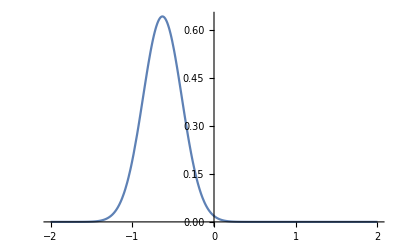

```mathematica
Plot[0.6420758824706843 ⅇ^(-8.894985249521016 (0.6311053293898136+x)^2),{x,-2,2}]
```

```mathematica
Plot[
{0.6420758824706843 ⅇ^(-8.894985249521016 (0.6311053293898136+x)^2),0.6420758824706843 ⅇ^(-8.894985249521016 (0.6311053293898136+x)^2),4.989257884390197 ⅇ^(-204.48361664622482 (0.8919714888655721+x)^2)}
,{x,-2,2},PlotLegends->"Expressions",PlotTheme->"Marketing"]
```

-Graphics-

```mathematica
Plot[
{0.6420758824706843 ⅇ^(-8.894985249521016 (0.6311053293898136+x)^2),0.6420758824706843 ⅇ^(-8.894985249521016 (0.6311053293898136+x)^2),4.989257884390197 ⅇ^(-204.48361664622482 (0.8919714888655721+x)^2)}
,{x,-2,2},PlotLegends->"Expressions",PlotTheme->"Marketing",PlotRange->Full]
```

-Graphics-

```mathematica
0.6420758824706843 ⅇ^(-8.894985249521016 (0.6311053293898136+x)^2)+4.989257884390197 ⅇ^(-204.48361664622482 (0.8919714888655721+x)^2)
```

```mathematica
Plot[
{0.6420758824706843 ⅇ^(-8.894985249521016 (0.6311053293898136+x)^2)+4.989257884390197 ⅇ^(-204.48361664622482 (0.8919714888655721+x)^2),0.6420758824706843 ⅇ^(-8.894985249521016 (0.6311053293898136+x)^2),4.989257884390197 ⅇ^(-204.48361664622482 (0.8919714888655721+x)^2)}
,{x,-2,2},PlotLegends->"Expressions",PlotTheme->"Marketing",PlotRange->Full]
```

-Graphics-

```mathematica
FindDistribution[Map[Last,Out[8][[-100;;]]]]
```

MixtureDistribution[{0.520602,0.479398},{NormalDistribution[-0.926621,0.035806],NormalDistribution[-0.555129,0.322961]}]

```mathematica
PDF[MixtureDistribution[{0.5206015249769534,0.47939847502304644},{NormalDistribution[-0.9266207402567049,0.03580601784928419],NormalDistribution[-0.5551285184492281,0.32296051366737544]}],x]
```

0.592185 ⅇ^(-4.7937 (0.555129+x)^2)+5.80042 ⅇ^(-389.994 (0.926621+x)^2)

```mathematica
FullSimplify[0.5921848422734387 ⅇ^(-4.793703295618576 (0.5551285184492281+x)^2)+5.800420488784437 ⅇ^(-389.994027984735 (0.9266207402567049+x)^2)]
```

0.592185 ⅇ^(-4.7937 (0.555129+x)^2)